```mathematica
i = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫E^((2 π I (w-y)^2)/(2 * D1 * λ))*E^((2 π I (y-z)^2)/(2 * D2 * λ))ⅆy;
```

```mathematica
abs2 = i * Conjugate[i]
```

-1/(√2 √(D1+D2))(1/4-ⅈ/4) (-1)^(3/4) √D1 √D2 ⅇ^((2 ⅈ D1 π)/λ+(2 ⅈ D2 π)/λ+(ⅈ π (w-z)^2)/((D1+D2) λ)+Conjugate[(2 ⅈ D1 π)/λ+(2 ⅈ D2 π)/λ+(ⅈ π (w-z)^2)/((D1+D2) λ)]) √λ Conjugate[(√D1 √D2 √λ)/(√(D1+D2))] Erf[(1+ⅈ) √(π/2) Conjugate[(D2 (-w+y)+D1 (y-z))/(√D1 √D2 √(D1+D2) √λ)]] Erfi[((-1)^(1/4) √π (D2 (-w+y)+D1 (y-z)))/(√D1 √D2 √(D1+D2) √λ)]

```mathematica
D1 = 380;
D2 = 500;
λ = .000546;
```

```mathematica
abs2
```

(-3.6048×10^-18-0.0294716 ⅈ) ⅇ^((0.+0. ⅈ)+(0.+6.53845 ⅈ) (w-z)^2-(0.+6.53845 ⅈ) (Conjugate[w]-Conjugate[z])^2) Erf[(0.00414806+0.00414806 ⅈ) Conjugate[500 (-w+y)+380 (y-z)]] Erfi[(0.00414806+0.00414806 ⅈ) (500 (-w+y)+380 (y-z))]

```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
counts1 = Import["2014_double_slit_bulb_counts.csv"];
counts1;
```

NonlinearModelFit::nrlnum: The function value {-5.97053 - 4.64592×10^-14\ ⅈ, -6.97053 - 4.64592×10^-14\ ⅈ, -1.97053 - 4.64592×10^-14\ ⅈ, -4.97053 - 4.64592×10^-14\ ⅈ, « 44 », -254.971 - 4.64592×10^-14\ ⅈ, -302.971 - 4.64592×10^-14\ ⅈ, « 70 »} is not a list of real numbers with dimensions {120} at {w, y, z} = {0., 1915., 0.}.

General::ivar: -10 is not a valid variable.

General::ivar: -9.99959 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

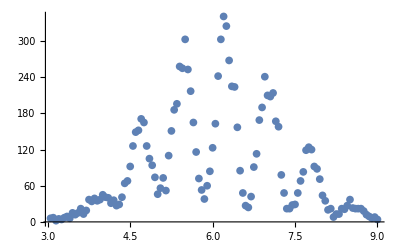

```mathematica
fit1 = NonlinearModelFit[counts1,abs2,{{w,0},{y,1915},{z,0}}, x];
plot1 = Plot[fit1[x], {x, -10, 10},PlotRange->All]
Show[ListPlot[counts1], plot1]
```